```mathematica
L =ToExpression[Import["/Users/jeremy/blog/machine-learning/neural-networks/sine.txt"]];
```

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

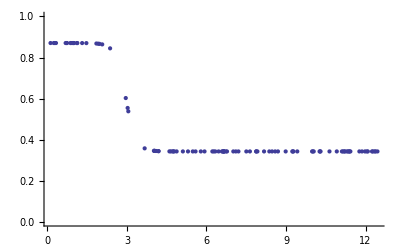
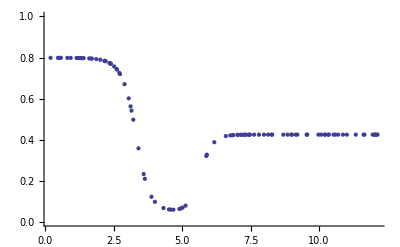
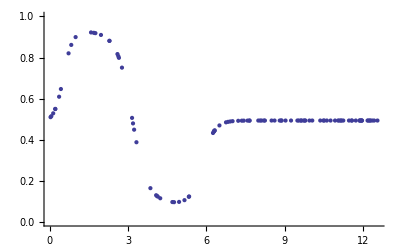
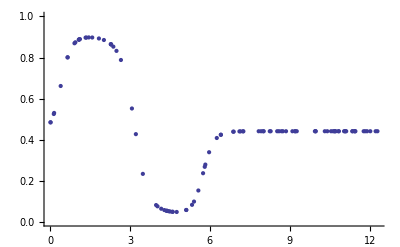
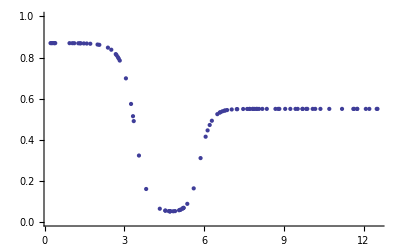
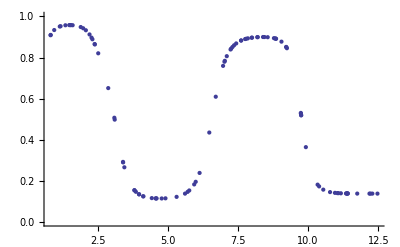
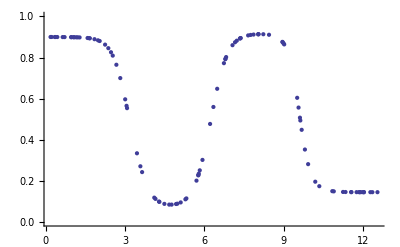
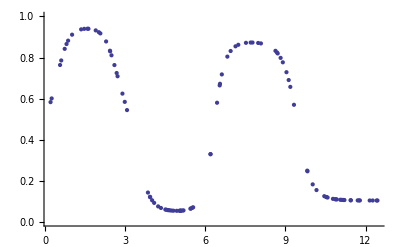
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListPlot[Null,PlotRange→{0,1}]}

```mathematica
plots = Table[ListPlot[x,PlotRange->{0,1}],{x,L}]
```

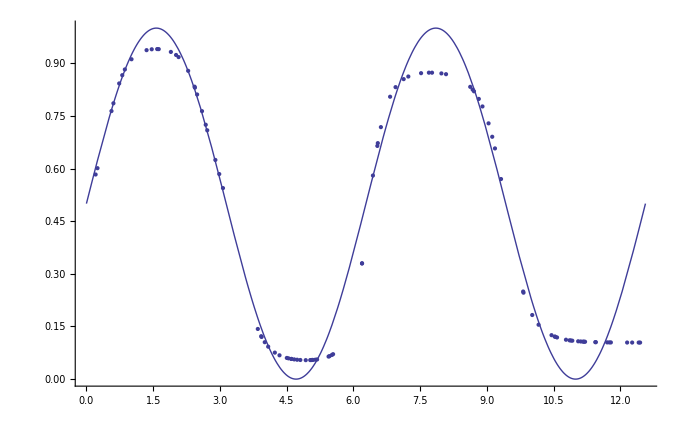

```mathematica
Show[ListPlot[L⟦8⟧], Plot[0.5*(1+Sin[x]),{x,0,4*Pi}]]
```

```mathematica
K={{1.09073434774,0.950824776453},{0.71969661792,0.825451386581},{1.63530033477,0.987092969716},{0.677347290087,0.810658219063},{6. 13662560256,0.357457972977},{6.13349797247,0.357305086163},{3.86879491547,0.183917550373},{0.62854132767,0.792892088559},{5.85374356443,0. 326758745921},{4.34873788763,0.0329897023272},{3.88928052566,0.17710167223},{5.71095569989,0.287119835226},{5.74086438266,0.297452940114},{0.131021621159,0.553611321365},{0.389005054513,0.687051242174},{1.92493539541,0.970214560858},{5.8965832318,0.334529933935},{1.50716456833,0.987845111755},{0.330908681391,0.656999014912},{5.83892758731,0.323689247316},{0.178900478229,0.577336876619},{5.02262822571,0. 02198169245},{4.69861048929,0.0141990172108},{5.77549979922,0.307988982641},{0.312325972013,0.64720986725},{5.97945640223,0.345687130603},{2.73925151616,0.695516196056},{1.87299802868,0.9760081982},{1.1690158384,0.967692520841},{2.93162862813,0.592022699767},{4.40248078204,0. 0265358464103},{5.22074574317,0.0516379469269},{4.51720738782,0.0184377719431},{2.05138085009,0.946642920637},{1.47139249538,0. 987606549651},{4.48206160659,0.0202815913721},{2.90366847921,0.608872457895},{4.32888657434,0.0359547290079},{1.70840673996,0.985442958323},{0.586598833689,0.776758405856},{3.23276938649,0.404456769634},{5.92809662182,0.339313565787},{2.70573372556,0.710448879198},{4.09365253263,0.100623589291},{6.04048614733,0.351406268969},{2.2370840717,0.885929430776},{6.12204216254,0.35672318179},{0.0939275056903,0.536113160912},{3.57984239834,0.265434883113},{0.625247785634,0.791657036091},{5.29118443674,0.0740429205919},{3.59807951837,0.260341686674},{3. 10095033826,0.4838696041},{5.8112938588,0.317383068542},{1.54502106977,0.987877768854},{1.11960800863,0.957874954452},{0.719344612106,0. 825330048702},{5.42974644343,0.141264699147},{4.08613320516,0.103454765732},{6.05913863149,0.352827303656},{3.85692556947,0.187763749016},{1.8062974287,0.981122660337},{5.0885339587,0.0279623460123},{0.101992690048,0.539844254917},{4.99716748198,0.0203153124274},{2.10568345883,0.931689766486},{1.95300121665,0.966247797739},{4.91057762201,0.0164940123355},{1.33551600326,0.984135904908},{1.21160287585,0. 974013319545},{4.34245066877,0.0338918820064},{2.55886600174,0.767836547308},{2.26786243914,0.874192147719},{0.911026633105,0.891773097681},{1.82242618127,0.980084001576},{1.16750426319,0.967433322215},{0.146660072526,0.561231889702},{3.87737235373,0.181091216657},{5.06425493965,0.0254373737863},{3.32296823083,0.358302518245},{1.10609758359,0.954695958967},{0.428944968254,0.706957367134},{2.17522775332,0. 908737248131},{5.66532141522,0.269029605447},{1.50149245647,0.987821287721},{6.13600274652,0.35742772599},{1.13960542836,0.962188148785},{0.476160139496,0.729422677738},{0.169664228975,0.572673138768},{3.42167363644,0.316640257771},{5.83981650236,0.323879339476},{1.93340185153,0.96908518394},{0.98687244643,0.918685496211},{4.80251379457,0.0143811718973},{3.14707068734,0.454846620154},{1.23449363215,0.97669682295},{6.05362584727,0.352421420161},{6.13895172554,0.357570062887},{2.34407080237,0.845165639123},{5.991903395,0.347001249775}};
```

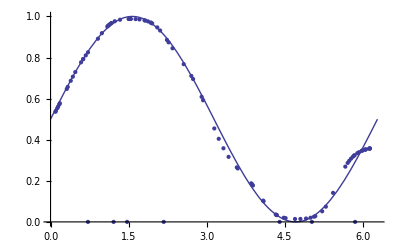

```mathematica
Show[Plot[0.5 * (1+Sin[x]),{x,0,2*Pi}],ListPlot[K]]
```